## Maximum copula

```mathematica
A=15;Plot3D[c[x,y,A],{x,0,1},{y,0,1},PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
SeedRandom[];
```

```mathematica
Y=.
```

{0.651,Null}

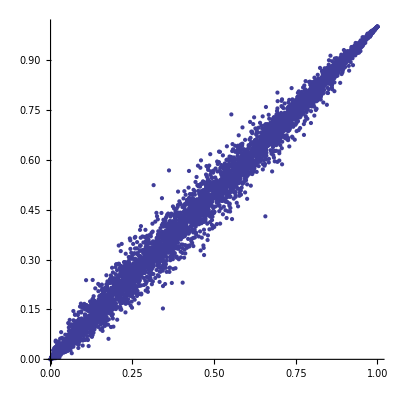

```mathematica
U={};A=15;
Timing[For[i=0,i<5000,i++,
x=RandomReal[];
y=f[x,RandomReal[],A];
AppendTo[U,{x,y}]]]
ListPlot[U,AspectRatio->1]
```

```mathematica
M={};m={};l=Length[U];h=1/15;For[i=0,i≤1,i+=h,
For[j=0,j≤1,j+=h,
AppendTo[m,Length[Select[U,#[[1]]≤i && #[[2]]≤j&]]/l-c[i,j,A]//N]
AppendTo[M,{i,j,Length[Select[U,#[[1]]≤i && #[[2]]≤j&]]/l}//N]
]
];m=Sort[m];
```

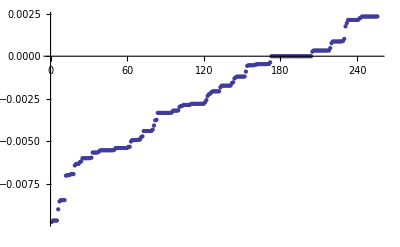

```mathematica
ListPlot[Transpose[m][[3]]]
```

```mathematica
ListPlot3D[M]
```

-Graphics3D-

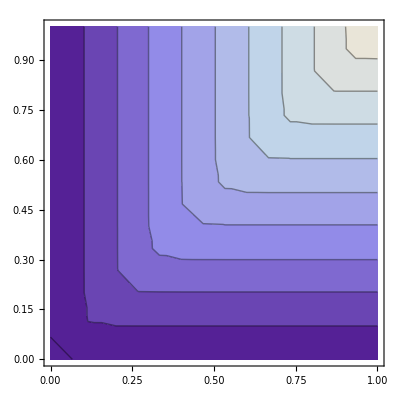

```mathematica
ListContourPlot[M]
```

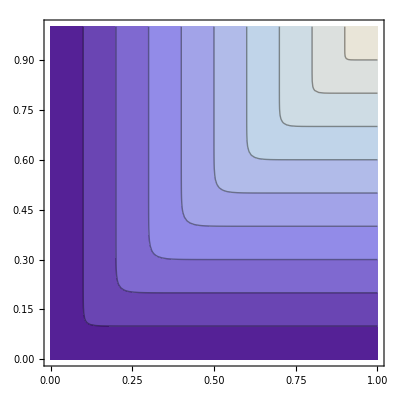

```mathematica
ContourPlot[c[x,y,15],{x,0,1},{y,0,1}]
```

```mathematica
f=Compile[{{x,_Real},{Z,_Real},{A,_Real}},ⅇ^(-(-(-Log[x])^A+((-1+A) ProductLog[((-x Z (-Log[x])^-A Log[x])^(-1/(-1+A)))/(-1+A)])^A)^(1/A))];
```

```mathematica
c[x_,y_,a_]:=Exp[-((-Log[x])^a+(-Log[y])^a)^(1/a)]
```

SetDelayed::write: Tag Rational in 1/15[x_, y_, a_] is Protected.

$Failed

```mathematica
c=.
```

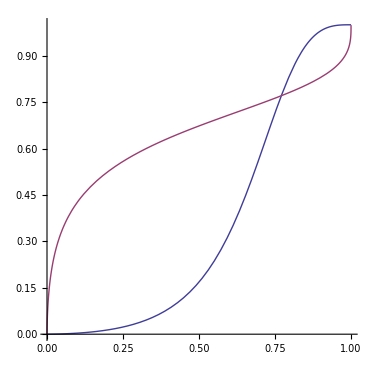

```mathematica
xx=0.7;A=3;Plot[{D[c[x,y,A],x]/.x->xx,f[y,A,xx]},{y,0,1},PlotRange->All,AspectRatio->1]
```

```mathematica
D[c[x,y,A],x]
```

```mathematica
f[AA,BB,CC]
```

ⅇ^(-(-(-Log[CC])^BB+((-1+BB) ProductLog[((-AA CC (-Log[CC])^-BB Log[CC])^(-1/(-1+BB)))/(-1+BB)])^BB)^(1/BB))

```mathematica
Solve[D[c[x,y,A],x]==Z,y]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→ⅇ^(-(-(-Log[x])^A+((-1+A) ProductLog[((-x Z (-Log[x])^-A Log[x])^(-1/(-1+A)))/(-1+A)])^A)^(1/A))}}

```mathematica
$Assumptions=a>1 && 0<Z<1 && 0<x<1
```

a>1&&0<Z<1&&0<x<1

```mathematica
a=.
```

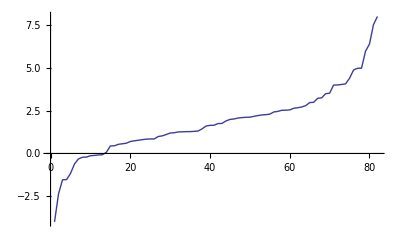

82

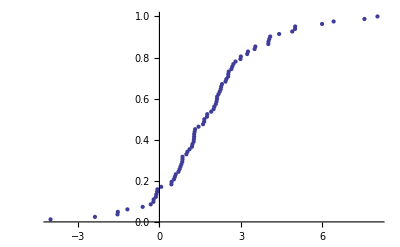

```mathematica
U=Sort[RandomReal[NormalDistribution[2,2],82]];
ListPlot[U,Joined->True]
n=Length[U]
F=Table[{U[[i]],i/n},{i,1,n}];
ListPlot[F]
```

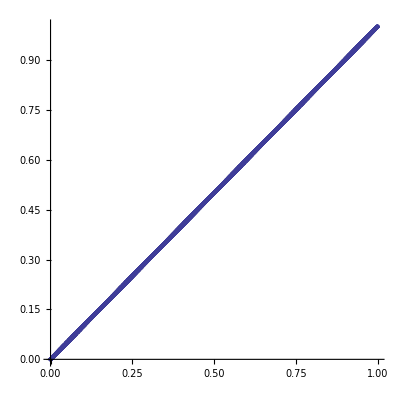

```mathematica
ListPlot[U,AspectRatio->1]
```

```mathematica
F[a_,b_]:=10000-Sort[Tally[UnitStep[a-#1[[2]]]UnitStep[b-#1[[1]]]&/@U],#1[[1]]<#2[[1]]&][[1,2]]
```

```mathematica
Sort[Tally[UnitStep[20/20-#1[[2]]]UnitStep[20/20-#1[[1]]]&/@U],#1[[1]]<#2[[1]]&]
```

{{1,10000}}

```mathematica
n=40;G={};
For[i=0,i<n,i++,
For[j=0,j<n,j++,
AppendTo[G,{i/n,j/n,F[i/n,j/n]}];
]]
```

```mathematica
G[[3]]
```

{0,1/10,0}

```mathematica
ListPlot3D[G,PlotRange->All,BoxRatios->{1,1,1}]
```

-Graphics3D-